```mathematica
G[z_, λ_, n_, M_] = Exp[-λ*(M-2)]*((1-Exp[-λ])*Exp[λ*z] + 1)^(M-2)*((1-Exp[-(n-(M-1)*λ)])Exp[λ*(z-1)] + Exp[-(n-(M-1)*λ)])*((1-Exp[-λ])Exp[(n-(M-1)*λ)*(z-1)] + Exp[-λ])
```

```mathematica
ⅇ^(-(-2+M) λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)))
```

ⅇ^((2-M) λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)))

```mathematica
Simplify[ⅇ^((2-M) λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)))]
```

ⅇ^(-n+λ-M λ) (ⅇ^((-1+M) λ)-ⅇ^((-2+M+z) λ)+ⅇ^(n+(-1+z) λ)) (1+ⅇ^((-1+z) λ) (-1+ⅇ^λ))^(-2+M) (1+ⅇ^((-1+z) (n+λ-M λ)) (-1+ⅇ^λ))

```mathematica
D[(ⅇ^((2-M) λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)))), z]
```

ⅇ^((2-M) λ+(-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) λ+ⅇ^((2-M) λ+z λ) (1-ⅇ^-λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-3+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ))) (-2+M) λ+ⅇ^((2-M) λ+(-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ))) (n-(-1+M) λ)

```mathematica
∂_z %2
```

ⅇ^((2-M) λ+(-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) λ^2+2 ⅇ^((2-M) λ+(-1+z) λ+z λ) (1-ⅇ^-λ) (1-ⅇ^(-n+(-1+M) λ)) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-3+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (-2+M) λ^2+ⅇ^((2-M) λ+z λ) (1-ⅇ^-λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-3+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ))) (-2+M) λ^2+ⅇ^((2-M) λ+2 z λ) (1-ⅇ^-λ)^2 (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-4+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ))) (-3+M) (-2+M) λ^2+2 ⅇ^((2-M) λ+(-1+z) λ+(-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ) (1-ⅇ^(-n+(-1+M) λ)) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) λ (n-(-1+M) λ)+2 ⅇ^((2-M) λ+z λ+(-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)^2 (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-3+M) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ))) (-2+M) λ (n-(-1+M) λ)+ⅇ^((2-M) λ+(-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ))) (n-(-1+M) λ)^2

```mathematica
Simplify[%3]
```

ⅇ^(-(-2+M) λ) (1+ⅇ^((-1+z) λ) (-1+ⅇ^λ))^(-4+M) (2 ⅇ^(-n+2 (-2+z) λ) (-1+ⅇ^λ) (ⅇ^n-ⅇ^((-1+M) λ)) (ⅇ^λ-ⅇ^(z λ)+ⅇ^(λ+z λ)) (1-ⅇ^((-1+z) (n+λ-M λ))+ⅇ^(λ+(-1+z) (n+λ-M λ))) (-2+M) λ^2+ⅇ^(-n+(-3+z) λ) (-1+ⅇ^λ) (ⅇ^((-1+M) λ)-ⅇ^((-2+M+z) λ)+ⅇ^(n+(-1+z) λ)) (ⅇ^λ-ⅇ^(z λ)+ⅇ^(λ+z λ)) (1-ⅇ^((-1+z) (n+λ-M λ))+ⅇ^(λ+(-1+z) (n+λ-M λ))) (-2+M) λ^2+ⅇ^(-n-3 λ+2 z λ) (-1+ⅇ^λ)^2 (ⅇ^((-1+M) λ)-ⅇ^((-2+M+z) λ)+ⅇ^(n+(-1+z) λ)) (1-ⅇ^((-1+z) (n+λ-M λ))+ⅇ^(λ+(-1+z) (n+λ-M λ))) (-3+M) (-2+M) λ^2+ⅇ^((-2+z) λ) (1-ⅇ^(-n+(-1+M) λ)) (1+ⅇ^((-1+z) (n+λ-M λ)) (-1+ⅇ^λ)) (λ+ⅇ^((-1+z) λ) (-1+ⅇ^λ) λ)^2+2 ⅇ^(n (-2+z)+(-5+M+2 z-M z) λ) (-1+ⅇ^λ) (-ⅇ^n+ⅇ^((-1+M) λ)) (ⅇ^λ-ⅇ^(z λ)+ⅇ^(λ+z λ))^2 λ (-n+(-1+M) λ)-2 ⅇ^(n (-2+z)+(-4+M+2 z-M z) λ) (-1+ⅇ^λ)^2 (ⅇ^((-1+M) λ)-ⅇ^((-2+M+z) λ)+ⅇ^(n+(-1+z) λ)) (ⅇ^λ-ⅇ^(z λ)+ⅇ^(λ+z λ)) (-2+M) λ (-n+(-1+M) λ)+ⅇ^(n (-2+z)+(-4+M+z-M z) λ) (-1+ⅇ^λ) (ⅇ^((-1+M) λ)-ⅇ^((-2+M+z) λ)+ⅇ^(n+(-1+z) λ)) (ⅇ^λ-ⅇ^(z λ)+ⅇ^(λ+z λ))^2 (n+λ-M λ)^2)

```mathematica
%4/.z-> 1
```

ⅇ^(-(-2+M) λ) (ⅇ^λ)^(-4+M) (ⅇ^λ (-1+ⅇ^λ) (-2+M) λ^2+2 ⅇ^(-n+λ) (-1+ⅇ^λ) (ⅇ^n-ⅇ^((-1+M) λ)) (-2+M) λ^2+(-1+ⅇ^λ)^2 (-3+M) (-2+M) λ^2+(1-ⅇ^(-n+(-1+M) λ)) (λ+(-1+ⅇ^λ) λ)^2+2 ⅇ^(-n+λ) (-1+ⅇ^λ) (-ⅇ^n+ⅇ^((-1+M) λ)) λ (-n+(-1+M) λ)-2 (-1+ⅇ^λ)^2 (-2+M) λ (-n+(-1+M) λ)+ⅇ^λ (-1+ⅇ^λ) (n+λ-M λ)^2)

```mathematica
Simplify[%5]
```

ⅇ^(-n-(2+M) λ) (ⅇ^λ)^M (ⅇ^(n+2 λ) n^2+ⅇ^(λ+M λ) λ (-2 n+λ)-2 ⅇ^(M λ) λ (-n+λ)-ⅇ^n (-2+M) λ (-2 n+λ+M λ)-ⅇ^(n+λ) (n^2+2 (-2+M) n λ+(1+M-M^2) λ^2))

```mathematica
Simplify[ⅇ^(-(-2+M) λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)))]
```

ⅇ^(-n+λ-M λ) (ⅇ^((-1+M) λ)-ⅇ^((-2+M+z) λ)+ⅇ^(n+(-1+z) λ)) (1+ⅇ^((-1+z) λ) (-1+ⅇ^λ))^(-2+M) (1+ⅇ^((-1+z) (n+λ-M λ)) (-1+ⅇ^λ))

```mathematica
Simplify[ⅇ^(-(-2+M) λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)))]
```

```mathematica
ⅇ^(-n+λ-M λ) (ⅇ^((-1+M) λ)-ⅇ^((-2+M+z) λ)+ⅇ^(n+(-1+z) λ)) (1+ⅇ^((-1+z) λ) (-1+ⅇ^λ))^(-2+M) (1+ⅇ^((-1+z) (n+λ-M λ)) (-1+ⅇ^λ))//TeXForm
```

e^{\lambda -\lambda  M-n} \left(\left(e^{\lambda }-1\right) e^{\lambda  (z-1)}+1\right)^{M-2} \left(e^{\lambda  (M-1)}-e^{\lambda  (M+z-2)}+e^{n+\lambda  (z-1)}\right) \left(\left(e^{\lambda }-1\right)
   e^{(z-1) (\lambda -\lambda  M+n)}+1\right)

```mathematica
G[0, λ, n, M]
```

ⅇ^(-(-2+M) λ) (2-ⅇ^-λ)^(-2+M) (ⅇ^-λ+ⅇ^(-n+(-1+M) λ) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^-λ (1-ⅇ^(-n+(-1+M) λ)))

```mathematica
Simplify[ⅇ^(-(-2+M) λ) (2-ⅇ^-λ)^(-2+M) (ⅇ^-λ+ⅇ^(-n+(-1+M) λ) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^-λ (1-ⅇ^(-n+(-1+M) λ)))] //TeXForm
```

\frac{\left(2-e^{-\lambda }\right)^M e^{-\lambda  (M-2)-2 n} \left(-e^{\lambda  (M-1)}+e^{\lambda  M}+e^n\right)^2}{\left(1-2 e^{\lambda }\right)^2}

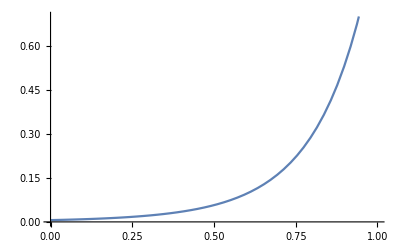

```mathematica
Plot[G[z, 1, 10, 10], {z, 0, 1}]
```

```mathematica
G[1, 1, 100, 20]
```

(1+(1-1/ⅇ) ⅇ)^18/ⅇ^18

```mathematica
N[(1+(1-1/ⅇ) ⅇ)^18/ⅇ^18]
```

1.

```mathematica
CoefficientList[Series[G[x, 1, 100, 20], {x, 0, 30}], x]
```

{((-1+2 ⅇ)^18 (-1+ⅇ+ⅇ^81)^2)/ⅇ^200,((-1+2 ⅇ)^17 (-100+381 ⅇ-461 ⅇ^2+7+20 ⅇ^163))/ⅇ^200,(((11)^16 1)/(2 ⅇ^200),25,1/ⅇ^18,(1/ⅇ^164+28+1)/ⅇ^18,(((2-1/ⅇ)^18 (1) (1)^2)/ⅇ^164+29+(2-1/ⅇ)^18 (1) ((81 (1) (1))/ⅇ^164+1/ⅇ^164))/ⅇ^18}
 |  |  |  |

```mathematica
ListLinePlot[%18]
```

ListLinePlot::lpn: 2.71828^(-1. (-2.+M) λ) (2.-1. 2.71828^(-1. λ))^(-2.+M) (2.71828^(-1. λ)+2.71828^(-1. n+(-1.+M) λ) (1.-1. 2.71828^(-1. λ))) (2.71828^(-1. n+(-1.+M) λ)+2.71828^(-1. λ) (1.-1. 2.71828^(Times[«2»]+Times[«2»]))) is not a list of numbers or pairs of numbers.

ListLinePlot[ⅇ^(-(-2+M) λ) (2-ⅇ^-λ)^(-2+M) (ⅇ^-λ+ⅇ^(-n+(-1+M) λ) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^-λ (1-ⅇ^(-n+(-1+M) λ)))]

```mathematica
g
```

```mathematica
CoefficientList[Series[G[x, 1, 40, 5], {x, 0, 60}], x]
```

{((-1+2 ⅇ)^3 (-1+ⅇ+ⅇ^36)^2)/ⅇ^80,((1)^2 (-40+10+5 1))/ⅇ^80,((1)11)/(2 ⅇ^80),55,1,1/ⅇ^3,1/ⅇ^3}
 |  |  |  |

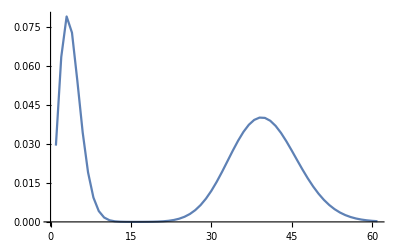

```mathematica
ListLinePlot[%4, PlotRange->All]
```

```mathematica
CoefficientList[Series[G[x, 10, 40, 5], {x, 0, 60}], x]
```

{((2-1/ⅇ^10)^3)/ⅇ^30,(30 (-1+ⅇ^10) (1)^2)/ⅇ^60,1/ⅇ^60,55,1/ⅇ^30,((1) 1^3)/ⅇ^30,((1) (2-1)^3)/ⅇ^30}
 |  |  |  |

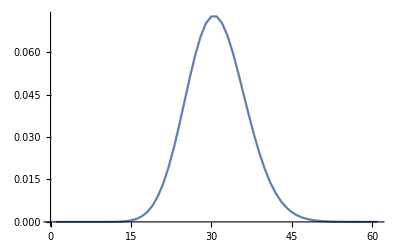

```mathematica
ListLinePlot[%6, PlotRange->All]
```

```mathematica
CoefficientList[Series[G[x, 0.5, 40, 5], {x, 0, 60}], x]
```

{0.222104,0.205124,0.111598,0.0459713,0.0156265,0.00457482,0.00118397,0.00027559,0.0000583931,0.000011364,2.05358×10^-6,3.76995×10^-7,1.68251×10^-7,3.52427×10^-7,9.60548×10^-7,2.49351×10^-6,6.07516×10^-6,0.000013933,0.0000301824,0.0000619484,0.000120803,0.00022438,0.000397863,0.000674881,0.0010972,0.00171262,0.00257072,0.00371625,0.00518096,0.00697468,0.00907746,0.0114344,0.0139548,0.0165165,0.0189758,0.0211807,0.0229878,0.0242776,0.0249679,0.0250223,0.0244528,0.0233161,0.0217054,0.0197385,0.0175439,0.0152485,0.0129669,0.0107934,0.00879804,0.00702604,0.00549938,0.00422054,0.00317717,0.00234689,0.00170169,0.00121157,0.000847316,0.000582247,0.000393249,0.00026113,0.000170529}

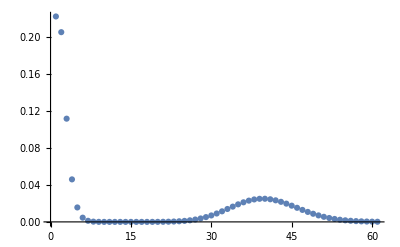

```mathematica
ListPlot[%8, PlotRange->All]
```

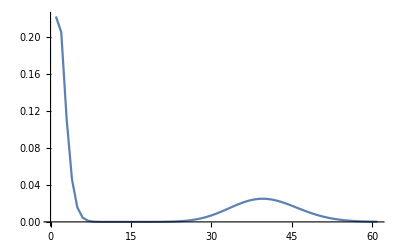

```mathematica
ListLinePlot[%8, PlotRange->All]
```

```mathematica
1-G[0, λ, n, M]
```

1-ⅇ^(-(-2+M) λ) (2-ⅇ^-λ)^(-2+M) (ⅇ^-λ+ⅇ^(-n+(-1+M) λ) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^-λ (1-ⅇ^(-n+(-1+M) λ)))

```mathematica
Simplify[1-ⅇ^(-(-2+M) λ) (2-ⅇ^-λ)^(-2+M) (ⅇ^-λ+ⅇ^(-n+(-1+M) λ) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^-λ (1-ⅇ^(-n+(-1+M) λ)))]
```

1-(ⅇ^(-2 n-(-2+M) λ) (2-ⅇ^-λ)^M (ⅇ^n-ⅇ^((-1+M) λ)+ⅇ^(M λ))^2)/((1-2 ⅇ^λ)^2)

```mathematica
Simplify[1-ⅇ^(-(-2+M) λ) (2-ⅇ^-λ)^(-2+M) (ⅇ^-λ+ⅇ^(-n+(-1+M) λ) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^-λ (1-ⅇ^(-n+(-1+M) λ)))]
```

(ⅇ^(-2 n-(-2+M) λ) (2-ⅇ^-λ)^M (ⅇ^n-ⅇ^((-1+M) λ)+ⅇ^(M λ))^2)/((1-2 ⅇ^λ)^2)

```mathematica
N[G[0, 0.1, 40,5]]
```

0.796689

```mathematica
ⅇ^(-(-2+M) λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)))
```

ⅇ^((2-M) λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)))

```mathematica
D[(ⅇ^((2-M) λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)))), z]
```

```mathematica
ⅇ^((2-M) λ+(-1+z) λ) (1-ⅇ^(-n+(-1+M) λ)) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) λ+ⅇ^((2-M) λ+z λ) (1-ⅇ^-λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-3+M) (ⅇ^-λ+ⅇ^((-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ)) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ))) (-2+M) λ+ⅇ^((2-M) λ+(-1+z) (n-(-1+M) λ)) (1-ⅇ^-λ) (1+ⅇ^(z λ) (1-ⅇ^-λ))^(-2+M) (ⅇ^(-n+(-1+M) λ)+ⅇ^((-1+z) λ) (1-ⅇ^(-n+(-1+M) λ))) (n-(-1+M) λ)
```

ⅇ^((2-M) λ) (1-ⅇ^(-n+(-1+M) λ)) (1+ⅇ^λ (1-ⅇ^-λ))^(-2+M) λ+ⅇ^(λ+(2-M) λ) (1-ⅇ^-λ) (1+ⅇ^λ (1-ⅇ^-λ))^(-3+M) (-2+M) λ+ⅇ^((2-M) λ) (1-ⅇ^-λ) (1+ⅇ^λ (1-ⅇ^-λ))^(-2+M) (n-(-1+M) λ)

```mathematica
Simplify[ⅇ^((2-M) λ) (1-ⅇ^(-n+(-1+M) λ)) (1+ⅇ^λ (1-ⅇ^-λ))^(-2+M) λ+ⅇ^(λ+(2-M) λ) (1-ⅇ^-λ) (1+ⅇ^λ (1-ⅇ^-λ))^(-3+M) (-2+M) λ+ⅇ^((2-M) λ) (1-ⅇ^-λ) (1+ⅇ^λ (1-ⅇ^-λ))^(-2+M) (n-(-1+M) λ)]
```

ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M (ⅇ^(n+λ) n-ⅇ^(M λ) λ+ⅇ^n (-n+λ))

```mathematica
ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M (ⅇ^(n+λ) n-ⅇ^(M λ) λ+ⅇ^n (-n+λ)) //TeXForm
```

\left(e^{\lambda }\right)^M e^{-\lambda  (M+1)-n} \left(-\lambda  e^{\lambda  M}+n e^{\lambda +n}+e^n (\lambda -n)\right)

```mathematica
Simplify[ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M (ⅇ^(n+λ) n-ⅇ^(M λ) λ+ⅇ^n (-n+λ))]
```

```mathematica
ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M (ⅇ^(n+λ) n-ⅇ^(M λ) λ+ⅇ^n (-n+λ))
```

ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M (ⅇ^(n+λ) n-ⅇ^(M λ) λ+ⅇ^n (-n+λ))

```mathematica
%8/.λ->n/(M-1)
```

ⅇ^(-n-((1+M) n)/(-1+M)) (ⅇ^(n/(-1+M)))^M (ⅇ^(n+n/(-1+M)) n-(ⅇ^((M n)/(-1+M)) n)/(-1+M)+ⅇ^n (-n+n/(-1+M)))

```mathematica
Simplify[ⅇ^(-n-((1+M) n)/(-1+M)) (ⅇ^(n/(-1+M)))^M (ⅇ^(n+n/(-1+M)) n-(ⅇ^((M n)/(-1+M)) n)/(-1+M)+ⅇ^n (-n+n/(-1+M)))]
```

(ⅇ^(-(2 M n)/(-1+M)) (ⅇ^(n/(-1+M)))^M (-ⅇ^n+ⅇ^((M n)/(-1+M))) (-2+M) n)/(-1+M)

```mathematica
FullSimplify[ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M (ⅇ^(n+λ) n-ⅇ^(M λ) λ+ⅇ^n (-n+λ))]
```

ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M (-ⅇ^(M λ) λ+ⅇ^n ((-1+ⅇ^λ) n+λ))

```mathematica
D[(ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M (ⅇ^(n+λ) n-ⅇ^(M λ) λ+ⅇ^n (-n+λ))), λ]
```

ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M (ⅇ^n-ⅇ^(M λ)+ⅇ^(n+λ) n-ⅇ^(M λ) M λ)+ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M (-1-M) (ⅇ^(n+λ) n-ⅇ^(M λ) λ+ⅇ^n (-n+λ))+ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M M (ⅇ^(n+λ) n-ⅇ^(M λ) λ+ⅇ^n (-n+λ))

```mathematica
Simplify[ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M (ⅇ^n-ⅇ^(M λ)+ⅇ^(n+λ) n-ⅇ^(M λ) M λ)+ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M (-1-M) (ⅇ^(n+λ) n-ⅇ^(M λ) λ+ⅇ^n (-n+λ))+ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M M (ⅇ^(n+λ) n-ⅇ^(M λ) λ+ⅇ^n (-n+λ))]
```

ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M (ⅇ^n (1+n-λ)+ⅇ^(M λ) (-1+λ-M λ))

```mathematica
g
```

```mathematica
Expand[ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M (ⅇ^n (1+n-λ)+ⅇ^(M λ) (-1+λ-M λ))]
```

```mathematica
FullSimplify[ⅇ^(-(1+M) λ) (ⅇ^λ)^M-ⅇ^(-n+M λ-(1+M) λ) (ⅇ^λ)^M+ⅇ^(-(1+M) λ) (ⅇ^λ)^M n-ⅇ^(-(1+M) λ) (ⅇ^λ)^M λ+ⅇ^(-n+M λ-(1+M) λ) (ⅇ^λ)^M λ-ⅇ^(-n+M λ-(1+M) λ) (ⅇ^λ)^M M λ]
```

```mathematica
NSolve[ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M (ⅇ^n (1+n-λ)+ⅇ^(M λ) (-1+λ-M λ))==0 &&  λ>0 && λ < n/(M-1), λ]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[ⅇ^(-n-(1+M) λ) (ⅇ^λ)^M (ⅇ^n (1+n-λ)+ⅇ^(M λ) (-1+λ-M λ))==0&&λ>0&&λ<n/(-1+M),λ]